1.13137×10^6 v

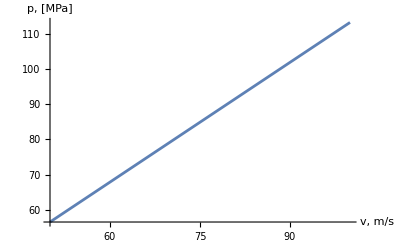

```mathematica
ClearAll["Global`*"];

m = 0.2 /1000;
S = 0.2*Power[10, -6];
alpha = 45;
deltaT  = 0.001;
vk = 0.6*v;
vHori = v*Cos[alpha °];
vkHori = vk*Cos[alpha °];
deltaPed = m*vHori + m*vkHori;
F= deltaPed/deltaT;
Pressure = F/S
Plot[Pressure*Power[10, -6], {v, 50, 100}, AxesLabel->{"v, m/s","p, [MPa]"}]
```